```mathematica
f[x_]=x^3-5x^2+3x+1/2x.b2+x-1
```

-1+4 x-(9 x.b2)/2+x.b3

```mathematica
f[x_]=(x^3-5*x^2+3*x+1)/(2*x^2+x-1)
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
g[x_]=x
```

x

```mathematica
h[x_]=Sin[x/3]-Cos[x^3/5]
```

-Cos[x^3/5]+Sin[x/3]

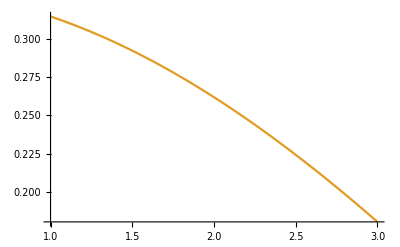

```mathematica
Plot[{h[x], h'[x]}, {x,1,3}]
```

```mathematica
h'[x]
```

1/3 Cos[x/3]

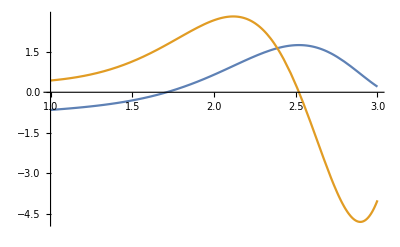

```mathematica
Plot[{h[x], h'[x]}, {x,1,3}]
```

```mathematica
j[x_]=E^-x
```

ⅇ^-x

```mathematica
k[x_]=Log[x]
```

Log[x]

```mathematica
NSolve[j[x]==k[x],x, Reals]
```

{{x→1.3098}}

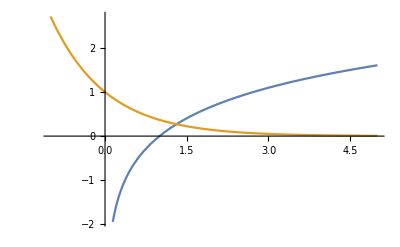

```mathematica
Plot[{k[x],j[x]}, {x,-1,5}]
```

```mathematica
j[1.3098]
```

0.269874

```mathematica
Sqrt[(1.3098)^2+(0.269879)^2]
```

1.33731

```mathematica
Plot[f[x],{x,-10,10}]
```

-Graphics-

```mathematica
Solve[2*x^2+x-1==0, x]
```

{{x→-1},{x→1/2}}

```mathematica
Clear[f]
```

```mathematica
f[x_]=(x^3-5x^2+3x+1)/(2x^2+x-1)
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

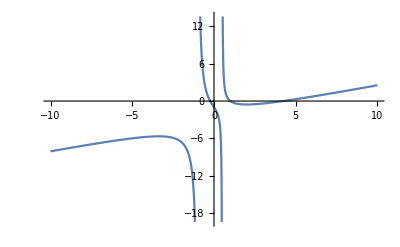

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Limit [f[x]/x, x->∞]
```

1/2

```mathematica
Limit[f[x]-(1/2)x, x->∞]
```

-11/4

```mathematica
Simplify [f[x]+f[-x]]
```

(-2+8 x^2-22 x^4)/(1-5 x^2+4 x^4)